```mathematica
Manipulate[Limit[Sin[a*x]/Sin[b*x],x->0],{a,1,5},{b,2,3}]
```

```mathematica
Limit[x^(x^x-1),x->0]
```

1

```mathematica
Series[x/(ⅇ^x-1),{x,0,10}]
```

1-x/2+x^2/12-x^4/720+x^6/30240-x^8/1209600+x^10/47900160+O[x]^11

```mathematica
Series[Log[Cos[x]],{x,0,10}]
```

-x^2/2-x^4/12-x^6/45-(17 x^8)/2520-(31 x^10)/14175+O[x]^11

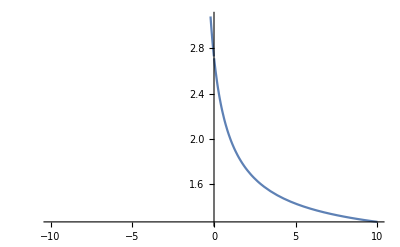

```mathematica
Plot[(1+x)^(1/x),{x,-10,10}]
```

```mathematica
Manipulate[ParametricPlot[{a*Cos[2t],a*Cos[3t]},{t,0,2*π}],{a,2,10}]
```

```mathematica
Manipulate[ParametricPlot[{a/(Cos[t])^3,a*(Tan[t])^3},{t,π/6,π/3}],{a,2,10}]
```

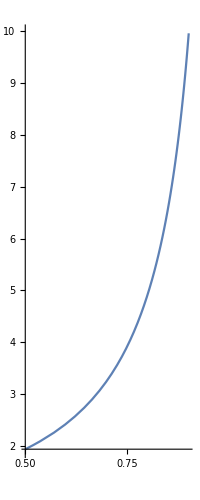

```mathematica
ParametricPlot[{(r-1)/r,(√(r^4-(r-1)^2))/r},{r,2,10}]
```

```mathematica
Manipulate[PolarPlot[(a*Tanh[t])/(t-1),{t,2,50}],{a,2,50}]
```

```mathematica
∫(ArcCot(ⅇ^x)/(ⅇ^x))ⅆx
```

ArcCot x

```mathematica
Integrate[ArcCot[Exp[x]]/(Exp[x]),x]
```

-ⅇ^-x ArcCot[ⅇ^x]+1/2 Log[1+ⅇ^(-2 x)]

```mathematica
Integrate[(x+1)/√(x^2+x+1),x]
```

√(1+x+x^2)+1/2 ArcSinh[(1+2 x)/(√3)]

```mathematica
NSum[((2*n-1)/(2^n)),{n,10}]
```

2.97754

```mathematica
Integrate[Exp[-x^2-y^2]*Cos[x^2+y^2],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

π/2

```mathematica
Integrate[Exp[-x^2-y^2]*Sin[x^2+y^2],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

π/2

```mathematica
A={{-2,8,6},{-4,10,6},{4,-8,-4}}
```

{{-2,8,6},{-4,10,6},{4,-8,-4}}

```mathematica
JordanDecomposition[A]⟦2⟧//MatrixForm
```

(0 | 0 | 0
0 | 2 | 0
0 | 0 | 2)

```mathematica
B={{2,0,1,1,0,0},{1,1,1,0,1,0},{-1,0,0,0,0,1},{0,0,0,2,0,1},{0,0,0,1,1,1},{0,0,0,-1,0,0}}
```

{{2,0,1,1,0,0},{1,1,1,0,1,0},{-1,0,0,0,0,1},{0,0,0,2,0,1},{0,0,0,1,1,1},{0,0,0,-1,0,0}}

```mathematica
JordanDecomposition[B]⟦2⟧//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Apart[(1/(x^4+4))]
```

(2-x)/(8 (2-2 x+x^2))+(2+x)/(8 (2+2 x+x^2))

```mathematica
Apart[x/((x^2-1)^2)]
```

1/(4 (-1+x)^2)-1/(4 (1+x)^2)

```mathematica
Factor[x^5+x^3+x^2+1]
```

(1+x) (1+x^2) (1-x+x^2)

```mathematica
Factor[x^3+2*x^2+4*x+1]
```

1+4 x+2 x^2+x^3

```mathematica
Manipulate[
ParametricPlot[{(R+r)*Cos[t]+r*Cos[t*(R+r)/r],(R+r)*Sin[t]+r*Sin[t*(R+r)/r]},{t,0,2*π}],{r,1,5},{R,7,10}]
```

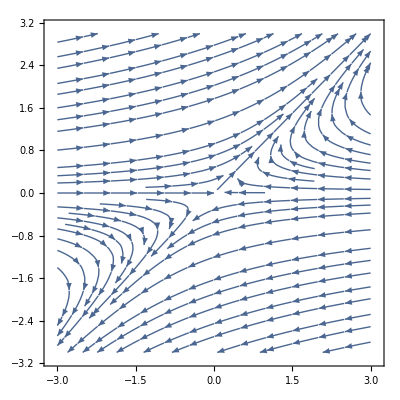

```mathematica
StreamPlot[{-2*x+3y,y},{x,-3,3},{y,-3,3}]
```

```mathematica
F[x_,y_,z_]:= x^2-y^2-2z
fx[x_,y_,z_]:=-(D[F[t,y,z],t]/.t->x)/(D[F[x,y,t],t]/.t->z)
fy[x_,y_,z_]:=-(D[F[x,t,z],t]/.t->y)/(D[F[x,y,t],t]/.t->z)
fxx[x_,y_,z_]:=(D[fx[xx,y,z],xx]/.xx->x )+(D[fx[x,y,zz],zz]/.zz->z)*(fx[x,y,z])
fxy[x_,y_,z_]:=(D[fx[x,yy,z],yy]/.yy->y)+(D[fx[x,y,zz],zz]/.zz->z)*(fy[x,y,z])
fyy[x_,y_,z_]:=(D[fy[x,yy,z],yy]/.yy->y)+(D[fy[x,y,zz],zz]/.zz->z)*(fy[x,y,z])
nn[x_,y_,z_]:=Cross[{1,0,fx[x,y,z]},{0,1,fy[x,y,z]}]/Norm[Cross[{1,0,fx[x,y,z]},{0,1,fy[x,y,z]}]]
iForm[x_,y_,z_]:=Det[({{{1,0,fx[x,y,z]}.{1,0,fx[x,y,z]}, {1,0,fx[x,y,z]}.{0,1,fy[x,y,z]}}, {{1,0,fx[x,y,z]}.{0,1,fy[x,y,z]}, {0,1,fy[x,y,z]}.{0,1,fy[x,y,z]}}})]
iiForm[x_,y_,z_]:=Det[({{{0,0,fxx[x,y,z]}.nn[x,y,z], {0,0,fxy[x,y,z]}.nn[x,y,z]}, {{0,0,fxy[x,y,z]}.nn[x,y,z], {0,0,fyy[x,y,z]}.nn[x,y,z]}})]
krivizna[x_,y_,z_]:=iiForm[x,y,z]/iForm[x,y,z]

kMax=Maximize[krivizna[x,y,z],F[x,y,z] == 0 && Abs[x]≤5 && Abs[y]≤5 && Abs[z]≤5,{x,y,z}]⟦1⟧;
kMin=Minimize[krivizna[x,y,z],F[x,y,z] == 0 && Abs[x]≤5 && Abs[y]≤5 && Abs[z]≤5,{x,y,z}]⟦1⟧;
kRes[x_,y_,z_]:=(krivizna[x,y,z]-kMin)/(1.4(kMax-kMin));

ContourPlot3D[x^2-y^2-2z==0,{x,-2,2},{y,-2,2},{z,-2,2},ColorFunction->Function[{x,y,z},Hue[kRes[x,y,z]]],ColorFunctionScaling->False]
```

-Graphics3D-

```mathematica
Manipulate[
poluperimetr[A1_,A2_,A3_]:=0.5*(Norm[A1-A2]+Norm[A1-A3]+Norm[A2-A3]);

radiusVpis[A1_,A2_,A3_]:=((poluperimetr[A1,A2,A3]-Norm[A1-A2])*(poluperimetr[A1,A2,A3]-Norm[A1-A3])*(poluperimetr[A1,A2,A3]-Norm[A2-A3])/poluperimetr[A1,A2,A3])^0.5;
kosinusAlpha[A1_,A2_,A3_]:=((Norm[A1-A3])^2+(Norm[A1-A2])^2-(Norm[A2-A3])^2)/(2*(Norm[A1-A3])*(Norm[A1-A2]));
kosinusAlphaPopolam[A1_,A2_,A3_]:=√((1+kosinusAlpha[A1,A2,A3])/2);
sinusAlphaPopolam[A1_,A2_,A3_]:=√(1-(kosinusAlphaPopolam[A1,A2,A3])^2);
tochkaKasania1[A1_,A2_,A3_]:=A1+((A3-A1)*radiusVpis[A1,A2,A3]*kosinusAlphaPopolam[A1,A2,A3])/((Norm[A3-A1])*sinusAlphaPopolam[A1,A2,A3]);
centrvpis[A1_,A2_,A3_]:=tochkaKasania1[A1,A2,A3] +({(A3-A1).{0,1},-(A3-A1).{1,0}}/Norm[A3-A1])*radiusVpis[A1,A2,A3];

tochkaKasania2[A1_,A2_,A3_]:=centrvpis[A1,A2,A3]+radiusVpis[A1,A2,A3]*({(A2-A1).{0,1},-(A2-A1).{1,0}}/Norm[A2-A1]);
tochkaKasania3[A1_,A2_,A3_]:=centrvpis[A1,A2,A3]+radiusVpis[A1,A2,A3]*({-(A2-A3).{0,1},(A2-A3).{1,0}}/Norm[A2-A3]);


rvpis=radiusVpis[spisok⟦1⟧,spisok⟦2⟧,spisok⟦3⟧];

Graphics[GraphicsComplex[spisok~Join~{tochkaKasania1[spisok⟦1⟧,spisok⟦2⟧,spisok⟦3⟧],centrvpis[spisok⟦1⟧,spisok⟦2⟧,spisok⟦3⟧],tochkaKasania2[spisok⟦1⟧,spisok⟦2⟧,spisok⟦3⟧],tochkaKasania3[spisok⟦1⟧,spisok⟦2⟧,spisok⟦3⟧]},{Thin,Line[{1,2,3,1}],Cyan,Thick,Line[{2,4}],Line[{3,6}],Line[{1,7}],Blue,Circle[5,rvpis],Orange,PointSize[Large],Point[{1,2,3,4,6,7}],Purple,Point[{5}]}],PlotRange->2],{{spisok,{{-1,-1},{1,-1},{0,1}}},Locator}

]
```